# Title The Quadratic Map

### Code for Chapter Opening Art

Module[{f,x},
f_r_[x_]:=r x (1-x);
Options[BifurcationPlot]={PlotPoints→2000,PlotStyle→{Black,PointSize[0.001]}};
Options[BifurcationPlotEfficient]={PlotPoints→2000,PlotStyle→{Black,PointSize[0.001]}};
BifurcationPlotEfficient[f_,{r_,a_,b_},{x_,x0_},{iter0_,iterShow_},opts___]:=Module[{ n,cf,rVals,data  },
{sty,n}={PlotStyle,PlotPoints}/.{opts}/.Options[BifurcationPlot];
makePts[{s_,v_}]:=({s,#}&)/@v;
cf=Compile[{r,x},Evaluate[f]];
com1=Compile[{rr}, (1+rr+√(-3-2 rr+rr^2))/(2 rr)];
com2=Compile[{rr}, (1+rr-√(-3-2 rr+rr^2))/(2 rr)];
iter[rr_]:=  Which[rr<3,{1-1/rr},
rr<3+45/100,{com1[rr], com2[rr]},True,NestList[cf[rr,#]&,Nest[cf[rr,#]&,x0,iter0],iterShow]];
rVals=Range[N[a],b,(b-a)/(n-1)];
data = {#,iter[#]}& /@ rVals;
ListPlot[Flatten[makePts/@data,1],Sequence@@FilterRules[{opts},Options[Graphics]], 
Frame→True,FrameTicks→{Automatic,Range[0,1,0.5], None, None},Axes→None,PerformanceGoal→"Speed",PlotStyle→sty]];
bifPlot=BifurcationPlotEfficient[f_r[x],{r,2.9,4},{x,0.5},{500,32}];
Manipulate[Column[{CobwebPlot[f_r[x],{x,0,1},0.1,{300,20},ImageSize→200],Show[bifPlot,GridLines→{{{r,Red}},{}},ImageSize→200]}],{{r,3.84},2.9,4,Appearance→"Labeled"},TrackedSymbols→{}, SaveDefinitions→True]]

## Title.Section Iterating Functions

```mathematica
NestList[Cos,1.5,20]
```

{1.5,0.0707372,0.997499,0.542405,0.85647,0.655109,0.792982,0.701724,0.76373,0.722261,0.750313,0.731476,0.74419,0.735637,0.741403,0.737522,0.740137,0.738376,0.739563,0.738763,0.739302}

```mathematica
NestList[Cos,Nest[Cos,1.5,100],10]
```

{0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

```mathematica
Cos[0.739085]
```

0.739085

```mathematica
NestList[Cos,1,5]
```

{1,Cos[1],Cos[Cos[1]],Cos[Cos[Cos[1]]],Cos[Cos[Cos[Cos[1]]]],Cos[Cos[Cos[Cos[Cos[1]]]]]}

CobwebPlot[f_,{x_,a_,b_},x0_,n_Integer, opts___]:=CobwebPlot[f,{x,a,b},x0,{0,n}, opts];

CobwebPlot[f_,{x_,a_,b_},x0_,{n0_,n_}, opts___]:=Module[{fcn,data,start},
fcn=Compile[x,f];
start=Nest[fcn,x0,n0];
data=NestList[fcn,start,n-1];
Show[Plot[f,{x,a,b},PlotStyle→{Black,Red,Thickness[0.004]}],
Graphics[{{Thickness[0.004],Black,
Line[Partition[Riffle[data,data],2,1]]},
{PointSize[Large],Point[{start,start}]},
{GrayLevel[0],Thickness[0.004],Dashing[{0.013,0.023}],Line[{{a,a},{b,b}}]}}],
opts,PlotRange→All, Frame→True,ImageSize→250, Axes→False, FrameTicks→{Automatic, Automatic, None,None}]]

CobwebPlot[Cos[x],{x,0,1.55},1.5,20]

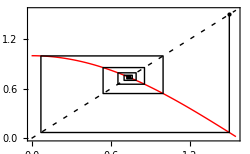

```mathematica
Table[Nest[Cos,c,100],{c,RandomReal[{-100,100},{10}]}]
```

{0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085,0.739085}

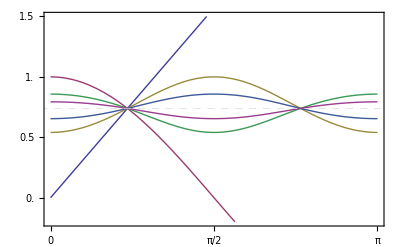

```mathematica
Plot[Evaluate[NestList[Cos,x,5]],{x,0,π},PlotRange->{-0.2,1.5},Frame->True,
Axes->False,PlotStyle->Thick,GridLines->{{},{{0.739,Dashed}}},FrameTicks->{Range[0,π,π/2],Range[-0.5,2,0.5],None,{0.739}}]
```

```mathematica
Options[CobwebPlot] = {WorkingPrecision->MachinePrecision};

CobwebPlot[f_,{x_,a_,b_},x0_,n_Integer, opts___]:=CobwebPlot[f,{x,a,b},x0,{0,n}, opts];

CobwebPlot[f_,{x_,a_,b_},x0_,{n0_,n_}, opts___]:=Module[{fcn,data,start,wp},
wp=WorkingPrecision/.{opts}/.Options[CobwebPlot];
fcn=If[wp===MachinePrecision,Compile[x,f],Function[{x}, N[f, wp]]];
start=Nest[fcn,x0,n0];
data=NestList[fcn,start,n-1];
Show[Plot[f,{x,a,b},Evaluate[Sequence @@ FilterRules[{opts},Options[Plot]]],PlotStyle->{Red,Thickness[0.004]}],
Graphics[{{Thickness[0.004],Black,
Line[Partition[Riffle[data,data],2,1]]},
{PointSize[Large],Point[{start,start}]},
{Dashing[{0.013,0.023}],Thickness[0.004],Line[{{a,a},{b,b}}]}}],
Sequence @@ FilterRules[{opts},Options[Graphics]],PlotRange->All, Frame->True, Axes->False, FrameTicks->{Automatic,Automatic,False,False}]]
```

```mathematica
Subscript[f, r_][x_]:=r x (1-x)
```

```mathematica
CobwebPlot[Subscript[f, 2][x],{x,0,1},0.1,10]
```

CobwebPlot[f_2[x],{x,0,1},0.1,10, ImageSize→250]

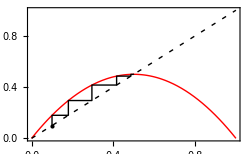

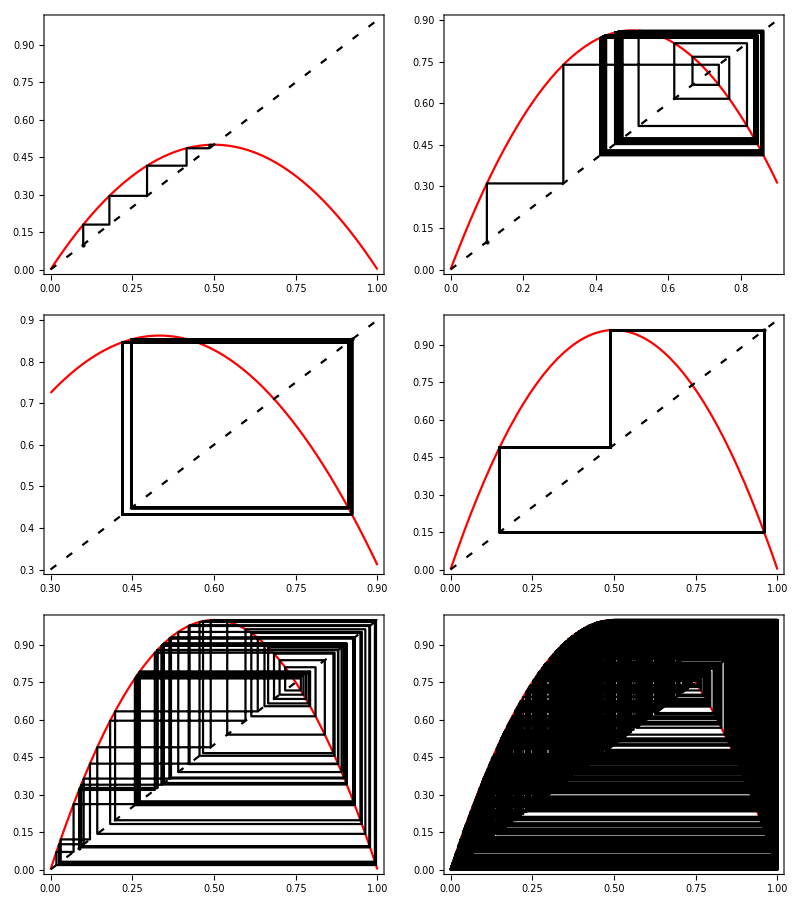

```mathematica
Grid[Partition[{
CobwebPlot[Subscript[f, 2][x],{x,0,1},0.1,10],
       CobwebPlot[Subscript[f, 3.45][x],{x,0,0.9},0.1,100],
       CobwebPlot[Subscript[f, 3.45][x],{x,0.3,0.9},0.1,{300,50}],
       CobwebPlot[Subscript[f, 3.839][x],{x,0,1},0.1,{150,50}],
       CobwebPlot[Subscript[f, 4][x],{x,0,1},0.1,{200,75}],
       CobwebPlot[Subscript[f, 4][x],{x,0,1},0.1,600]},2]]
```

```mathematica
GraphicsColumn[Table[GraphicsRow[{
CobwebPlot[Subscript[f, r][x],{x,0,1},0.1,100, PlotRange->{{0.2, 0.85},{0.3,0.85}}, FrameTicks->{{.3,.8},{.3,.8},None,None}],CobwebPlot[Nest[Subscript[f, r],x,2],{x,0,1},0.1,100, PlotRange->{{0.2, 0.85},{0.5,0.8}}, FrameTicks->{{.3,.8},{.3,.8},None,None}]},  AspectRatio-> 1/2,Frame->True,PlotRegion->{{0,1},{0,1}}, ImagePadding->Automatic, ImageSize->300,PlotLabel->StringForm["r = ``",PaddedForm[r,{3,2}]]],{r,2.9,3.1,0.05}]]
```

-Graphics-

```mathematica
Manipulate[Grid[{
{CobwebPlot[Nest[Subscript[f, r],x,2],{x,0,1},0.1,100, PlotRange->{{0.2, 1},{0.5,0.8}}],
CobwebPlot[Subscript[f, r][x],{x,0,1},0.1,100, PlotRange->{{0.2, 0.8},{0.3,0.75}}]}}],{r,2.9,3.3,0.01}]
```

## Title.Section The Four Flavors of Real Numbers

```mathematica
20/49+31/17
```

1859/833

```mathematica
1.3+1.12345678955555 10^-7//InputForm
```

1.300000112345679

```mathematica
Precision[%]
```

MachinePrecision

```mathematica
1.+1/10^17-1
```

0.

```mathematica
N[1+1/10^17-1]
```

1.×10^-17

```mathematica
(a=N[π,30])//InputForm
```

3.1415926535897932384626433832795028841971676788548462879281`30.

```mathematica
Precision[a^100000]
```

25.

```mathematica
Nest[Subscript[f, 4],N[1/10,30],30]//InputForm
```

0.32034249381837718430096359663`12.443814812333398

```mathematica
a=N[π/2+1/10^7,30];
Precision[Sin[a]]
```

36.8039

```mathematica
Sin[Interval[{-π,π}]]
```

Interval[{-1,1}]

```mathematica
g[x_] := Sin[x]+Cos[x];
g[Interval[{-π,π}]]
```

Interval[{-2,2}]

```mathematica
Nest[Subscript[f, 4],Interval[N[1/10,30]],30]
```

Interval[{0.320342493798,0.320342493839}]

```mathematica
N[Sin[10^50]]
```

-0.4805

```mathematica
N[Sin[10^50],20]
```

-0.78967249342931008271

```mathematica
Sin[Interval[N[10,75]]^50]
```

Interval[{-0.7896724934293100827103,-0.78967249342931008271028}]

```mathematica
$MaxExtraPrecision=500;
N[Sin[10^100],20]
```

-0.37237612366127668826

```mathematica
Nest[Subscript[f, 4], 0.1, 100]
```

0.372447

```mathematica
Nest[Subscript[f, 4],N[1/10,70],100]
```

0.9301089742

```mathematica
Log[10.,Numerator[Nest[Subscript[f, 4],1/10, 21]]]
```

1.46585×10^6

```mathematica
Nest[Subscript[f, 4], Interval[N[1/10, 100]], 100]
```

Interval[{0.930108974186554715591567623243613965116,0.9301089741865547155915676232436139651299}]

```mathematica
70-Round[Precision/@NestList[Subscript[f, 4],N[1/10,70],100]]
```

{0,0,0,1,1,2,3,4,4,4,6,6,6,10,10,10,10,10,10,11,11,12,12,14,14,14,16,16,16,16,18,18,19,19,21,21,21,21,24,24,24,24,24,25,26,26,27,29,29,29,29,30,32,32,32,32,33,33,34,35,36,36,37,37,38,38,39,39,40,41,41,42,44,44,44,44,46,46,46,48,48,48,49,49,50,50,51,52,52,53,54,54,54,55,56,57,57,57,59,59,59}

```mathematica
δ=10^-150;x0=1/10;
Table[Δ=Abs[Nest[Subscript[f, 4],N[x0-δ/2,200],n]-Nest[Subscript[f, 4],N[x0+δ/2,200],n]];Round[Log[10,Δ/δ]],{n,0,100}]
```

{0,1,1,1,1,2,2,2,3,3,3,4,2,3,3,4,4,5,6,6,6,7,6,7,7,7,8,8,9,9,9,9,10,9,10,11,11,10,11,11,12,13,13,13,13,14,13,14,14,15,15,15,15,16,16,17,17,17,18,18,18,18,19,19,19,20,20,20,21,21,21,21,22,22,22,22,23,23,23,23,24,24,25,25,25,26,26,26,27,27,27,28,28,28,28,29,29,29,30,30,30}

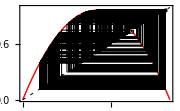
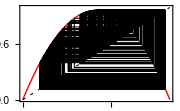

```mathematica
r=31/8;
Row[{CobwebPlot[Subscript[f, r][x],{x,0,1},1/10,{100,300}, PlotStyle->{Red,Thick}, ImageSize->180],Spacer[20],
        CobwebPlot[Subscript[f, r][x],{x,0,1},1/10,{100,300},WorkingPrecision->1000,PlotStyle->{Red,Thick}, ImageSize->180]}]
```

## Title.Section Attracting and Repelling Cycles

```mathematica
Clear[r];x/.Solve[Subscript[f, r][x]==x,x]
```

{0,(-1+r)/r}

```mathematica
Table[Sort[NestList[Subscript[f, 3.45],Nest[Subscript[f, 3.45],Random[],500],3]],{10}]
```

{{0.435794,0.444013,0.848278,0.851686},{0.433021,0.447048,0.847017,0.852827},{0.433015,0.447056,0.84702,0.852829},{0.434634,0.445263,0.847762,0.852163},{0.433007,0.447064,0.847016,0.852832},{0.433088,0.446973,0.847054,0.852799},{0.43853,0.441162,0.849464,0.850557},{0.433118,0.446928,0.847067,0.852783},{0.432991,0.447068,0.847009,0.852834},{0.433007,0.447064,0.847016,0.852832}}

```mathematica
(x/.FindRoot[Nest[Subscript[f, 3.45],x,4]==x,{x,#},AccuracyGoal->12]&)/@%⟦1⟧
```

{0.433992,0.445968,0.847468,0.852428}

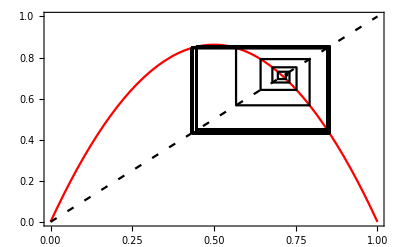

```mathematica
CobwebPlot[Subscript[f, 3.45][x],{x,0,1},49/69+0.01,100]
```

```mathematica
Subscript[f, 345/100][49/69]
```

49/69

```mathematica
Solve[Subscript[f, 345/100][x]==49/69]
```

{{x→20/69},{x→49/69}}

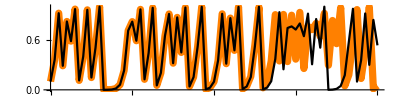

```mathematica
n=80;
orbit=Transpose[{Range[0,n],NestList[Subscript[f, 4],N[1/10,n],n]}];
orbit1=Transpose[{Range[0,n],NestList[Subscript[f, 4],N[1/10+1/10^17,n],n]}];
ListLinePlot[{orbit,orbit1},PlotStyle->{{Thickness[0.013],Orange},{Thickness[0.004],Black}},AspectRatio->0.25]
```

```mathematica
TrigIteration[n_, x0_]:=1/2(1- Cos[2^n ArcCos[1-2x0]])
```

```mathematica
N[{TrigIteration[5,1/10],Nest[Subscript[f, 4],1/10,5]}]
```

{0.585421,0.585421}

```mathematica
(x/.RSolve[{x[n+1]==4 x[n] (1-x[n]),x[0]==x0},x,n]⟦1⟧)[n]//Quiet
```

1/2 (1-Cos[2^n ArcCos[1-2 x0]])

```mathematica
TrigExpand[TrigIteration[n+1,x]==4 TrigIteration[n,x] (1-TrigIteration[n,x])]
```

True

```mathematica
fval=Subscript[f, 4][Sin[(π v)/2]^2];
Simplify[2/π ArcSin[√fval],0≤v≤1/2]
```

2 v

```mathematica
PowerExpand[Simplify[2/π ArcSin[√fval],1/2<v≤1],Assumptions->1/2<v≤1]
```

2-2 v

```mathematica
stringOp[bits_]:=If[bits⟦1⟧==0,Rest[bits],1-Rest[bits]]
Nest[stringOp,Flatten[Table[{0,1,0},{10}]],3]
```

{0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0,0,1,0}

```mathematica
v=FromDigits[{{{0,1,0}},0},2]
```

2/7

```mathematica
ToX[v_]:=Sin[(π v)/2]^2;
FromX[x_]:=2/π ArcSin[√x];
x0=ToX[v]
```

Sin[π/7]^2

```mathematica
CobwebPlot[Subscript[f, 4][x],{x,0,1},x0,10]
```

-Graphics-

```mathematica
v=31/64;
x0=ToX[v]
```

Sin[(31 π)/128]^2

```mathematica
N[NestList[Subscript[f, 4],N[x0,20],7],6]
```

{0.475466,0.99759,0.0096074,0.03806,0.14645,0.5,1.,0.}

```mathematica
CobwebPlot[Subscript[f, 4][x],{x,0,1},x0+10^-10,80,WorkingPrecision->200]
```

-Graphics-

## Title.Section Measuring Instability: The Lyapunov Exponent

```mathematica
Lyapunovλ[r_,x0_,n_,δ_]:=With[{prec=Max[2 n,-Log[10,δ] 2+20]},
Δ=Abs[Nest[Subscript[f, r],N[x0-δ/2,prec],n]-Nest[Subscript[f, r],N[x0+δ/2,prec],n]];N[1/n Log[Δ/δ],4]]/; Union[Precision /@ {r, x0, n,δ} ]== {∞}
```

```mathematica
Subscript[f, 4][.1]
```

0.36

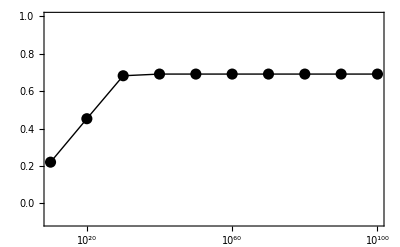

```mathematica
ListLinePlot[data=Table[{d,Lyapunovλ[4, 1/10,100,10^-d]}, {d,10,100,10}], Frame->True, Axes->False,PlotStyle->{Thick,Black}, PlotRange->{-0.1,1}, Epilog ->{PointSize[0.02], Point[data]}, FrameTicks -> {{#, HoldForm[10^#]} & /@ Range[20,200,20],Automatic, None, None}]
```

```mathematica
λByDer[r_,x0_,n_]:=1/n Log[Abs[D[Nest[Subscript[f, r],x,n], x]]]/.x->x0
{λByDer[4,0.1,10],Lyapunovλ[4,1/10,10,1/10^10]}
```

{0.709963,0.71}

```mathematica
Manipulate[r1=Rationalize[r];ListLinePlot[Table[{d,Lyapunovλ[r1, 1/10,100,10^-d]}, {d,10,100,10}], Frame->True, Axes->False,PlotStyle->{Thick,Black}, FrameTicks -> {{#, HoldForm[10^#]}& /@ Range[20,200,20],Automatic, None, None},PlotRange->{{5,105},{-3,1}}, PlotLabel-> StringForm["r = ``",N[r,3]]], {{r,4},2,4, 1./100}]
```

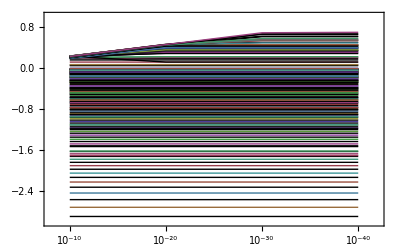

```mathematica
ListLinePlot[Table[Table[{d,Lyapunovλ[r,1/10,100,10^-d]},{d,10,40,10}],{r,2,4,1/100}],Frame->True,Axes->False,PlotStyle->{Thick,Black},FrameTicks->{({#1,HoldForm[10^-#1]}&)/@Range[10,40,10],Automatic,None,{0,{Log[2],"log 2"}}},PlotRange->{{8,42},{-3,1}}]
```

```mathematica
Monitor[ListLinePlot[Table[{r,Lyapunovλ[r,1/10,300,10^-100]},{r,1,4,3/20000 100}], Frame->True, PlotStyle->{Thickness[0.0001],Black},
PlotRange->All, Filling->{1->{0, Red}}], ProgressIndicator[r,{1,4}]]
```

Monitor[ListLinePlot[Table[{r,Lyapunovλ[r,1/10,300,10^-100]},{r,1,4,3/20000}], Frame→True, PlotStyle→{Thickness[0.0001],Black},
PlotRange→All, Filling→{1→{0,Black}},FrameTicks→{Automatic, Automatic, None, None},ImageSize→400, AspectRatio→0.4], ProgressIndicator[r,{1,4}]]

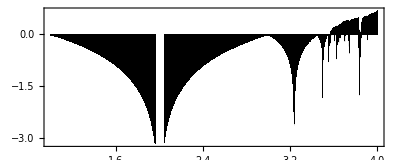

## Title.Section Bifurcations

```mathematica
cf=Compile[{{r,_Real,1},{x,_Real,1}},r+x];
cf[{1.,2.,3.},{2.,3.,4.}]
```

{3.,5.,7.}

```mathematica
cf=Compile[{{r,_Real,1},{x,_Real,1}},r x (1-x)];
rVals=Range[2.,4,(4-2)/(10-1)];
Transpose[NestList[cf[rVals,#1]&,Nest[cf[rVals,#1]&,(0.1&)/@rVals,10],4]]
```

{{0.5,0.5,0.5,0.5,0.5},{0.550001,0.55,0.55,0.55,0.55},{0.590894,0.590916,0.590906,0.59091,0.590909},{0.622448,0.626684,0.62387,0.62575,0.624499},{0.627918,0.674951,0.633799,0.670505,0.638237},{0.582761,0.756469,0.573141,0.761135,0.565627},{0.7,0.7,0.7,0.7,0.7},{0.882004,0.370037,0.828834,0.504421,0.888819},{0.516488,0.943417,0.201661,0.6082,0.900217},{0.147837,0.503924,0.999938,0.000246305,0.000984976}}

```mathematica
NestList[Subscript[f, 4],Nest[Subscript[f, 4],0.1,10],4]
```

{0.147837,0.503924,0.999938,0.000246305,0.000984976}

```mathematica
Column[Transpose[{rVals, Transpose[NestList[cf[rVals,#]&, Nest[cf[rVals, #]&, 
          Array[ 0.1 &,10] , 10], 4]]}] ]
```

{2.,{0.5,0.5,0.5,0.5,0.5}}
{2.22222,{0.550001,0.55,0.55,0.55,0.55}}
{2.44444,{0.590894,0.590916,0.590906,0.59091,0.590909}}
{2.66667,{0.622448,0.626684,0.62387,0.62575,0.624499}}
{2.88889,{0.627918,0.674951,0.633799,0.670505,0.638237}}
{3.11111,{0.582761,0.756469,0.573141,0.761135,0.565627}}
{3.33333,{0.7,0.7,0.7,0.7,0.7}}
{3.55556,{0.882004,0.370037,0.828834,0.504421,0.888819}}
{3.77778,{0.516488,0.943417,0.201661,0.6082,0.900217}}
{4.,{0.147837,0.503924,0.999938,0.000246305,0.000984976}}

```mathematica
Options[BifurcationPlot]={PlotPoints->2000,PlotStyle->{Black,PointSize[0.001]}};
BifurcationPlot[f_,{r_,a_,b_},{x_,x0_},{iter0_,iterShow_},opts___]:=Module[{sty,n,makePts,cf,rVals,data},
{sty,n}={PlotStyle,PlotPoints}/.{opts}/.Options[BifurcationPlot];
makePts[{s_,v_}]:=({s,#}&)/@v;
cf=Compile[{{r,_Real,1},{x,_Real,1}},Evaluate[f]];
rVals=Range[N[a],b,(b-a)/(n-1)];
data=Transpose[{rVals,Transpose[NestList[cf[rVals,#]&,Nest[cf[rVals,#1]&,Array[x0&,n],iter0], iterShow]]}];
Graphics[Append[Flatten[{sty}],Point[Flatten[makePts/@data,1]]],Sequence@@FilterRules[{opts},Options[Graphics]], 
AspectRatio->1/3,Frame->True,FrameTicks->{Automatic,Range[0,1,.5], None, None},Axes->None]];
```

```mathematica
BifurcationPlot[Subscript[f, r][x],{r,2.8,4},{x,0.5},{500,100},FrameTicks->{{3,3.45,3.57,3.839,4},Automatic,{{69/20, "69/20"}},None},GridLines->{{3,3.45,3.57,3.839},None}]
```

-Graphics-

```mathematica
Options[BifurcationPlotEfficient]={PlotPoints->2000,PlotStyle->{Black,PointSize[0.001]}};
BifurcationPlotEfficient[f_,{r_,a_,b_},{x_,x0_},{iter0_,iterShow_},opts___]:=Module[{ n,cf,rVals,data  },
{sty,n}={PlotStyle,PlotPoints}/.{opts}/.Options[BifurcationPlot];
makePts[{s_,v_}]:=({s,#}&)/@v;
cf=Compile[{r,x},Evaluate[f]];
com1=Compile[{rr}, (1+rr+√(-3-2 rr+rr^2))/(2 rr)];
com2=Compile[{rr}, (1+rr-√(-3-2 rr+rr^2))/(2 rr)];
iter[rr_]:=  Which[rr<3,{1-1/rr},
rr<3+45/100,{com1[rr], com2[rr]},True,NestList[cf[rr,#]&,Nest[cf[rr,#]&,x0,iter0],iterShow]];
rVals=Range[N[a],b,(b-a)/(n-1)];
data = {#,iter[#]}& /@ rVals;
ListPlot[Flatten[makePts/@data,1],Sequence@@FilterRules[{opts},Options[Graphics]], 
Frame->True,FrameTicks->{Automatic,Range[0,1,0.5], None, None},Axes->None,PerformanceGoal->"Speed",PlotStyle->sty]];
bifPlot=BifurcationPlotEfficient[Subscript[f, r][x],{r,2.9,4},{x,0.5},{500,32}];
```

```mathematica
Manipulate[Column[{CobwebPlot[Subscript[f, r][x],{x,0,1},0.1,{300,20},ImageSize->200],Show[bifPlot,GridLines->{{{r,Red}},{}},ImageSize->200]}],{{r,3.84},2.9,4,Appearance->"Labeled"}]
```

Manipulate[Column[{CobwebPlot[f_r[x],{x,0,1},0.1,{300,20},ImageSize→200],Show[bifPlot,GridLines→{{{r,Red}},{}},ImageSize→200]}],{{r,3.84},2.9,4,Appearance→"Labeled"},TrackedSymbols→{}, SaveDefinitions→True]

```mathematica
bifPts={3,3.45,3.54409,3.56441,3.56876,3.56969,3.56989,3.569943,3.5699451};
limitr=3.569945557391439;
logMin=Log[10,limitr-2.5];
n=2000; x0=0.1; iter0=1000;iterShow=64;
makePts[{s_,v_}]:=({s,#1}&)/@v;
cf=Compile[{{r,_Real,1},{x,_Real,1}},Evaluate[Subscript[f, r][x]]];
rValsLog=Range[logMin,-3,(-3-logMin)/(n-1)];
rVals=limitr-10^rValsLog;

data=Transpose[{-rValsLog,Transpose[NestList[cf[rVals,#]&,Nest[cf[rVals,#]&,Array[x0 &,n],iter0],iterShow]]}];

Graphics[{PointSize[0.0013],Point[Flatten[makePts/@data,1]]},Frame->True,AxesOrigin->{0,0.3},GridLines->{-Log[10,limitr-bifPts],None},FrameTicks->{({-#,NumberForm[limitr-10^#,4]} &)/@Log[10,limitr-bifPts],{0.3,0.6,0.9},None,None},PlotRange->{0.3,0.9}]
```

bifPts={3,3.45,3.54409,3.56441,3.56876,3.56969,3.56989,3.569943,3.5699451};
limitr=3.569945557391439;
logMin=Log[10,limitr-2.5];
n=2000; x0=0.1; iter0=1000;iterShow=64;
makePts[{s_,v_}]:=({s,#1}&)/@v;
cf=Compile[{{r,_Real,1},{x,_Real,1}},Evaluate[f_r[x]]];
rValsLog=Range[logMin,-3,(-3-logMin)/(n-1)];
rVals=limitr-10^rValsLog;

data=Transpose[{-rValsLog,Transpose[NestList[cf[rVals,#]&,Nest[cf[rVals,#]&,Array[x0&,n],iter0],iterShow]]}];

Graphics[{PointSize[0.0013],Point[Flatten[makePts/@data,1]]},Frame→True,AxesOrigin→{0,0.3},GridLines→{-Log[10,limitr-bifPts],None},FrameTicks→{({-#,NumberForm[limitr-10^#,4]} &)/@Log[10,limitr-bifPts],{0.3,0.6,0.9},None,None},PlotRange→{0.3,0.9}, ImageSize→400]

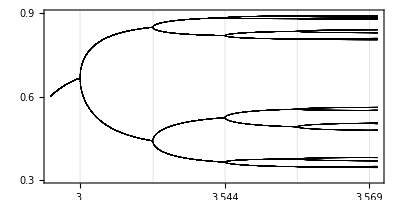

```mathematica
eFunc[x_]:=1/2 ⅇ/(ⅇ-1)(ⅇ^(-(2 x-1)^2)-1/ⅇ);
g[x_] := eFunc[Sin[π x/2]];
Plot[eFunc[x],{x,0,1}]
Plot[g[x],{x,0,1}]
```

GraphicsRow[{Plot[eFunc[x],{x,0,1},PlotStyle→{Black,Thick}, ImageSize→170, Frame→True, Axes→False, FrameTicks→ {Range[0,1, .2],Range[0,.5, .1], {}, {} } ],Plot[g[x],{x,0,1},PlotStyle→{Black,Thick}, ImageSize→170, Frame→True, Axes→False, FrameTicks→ {Range[0,1, .2],Range[0,.5, .1], {}, {} } ]}]

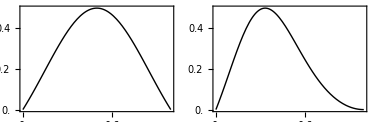

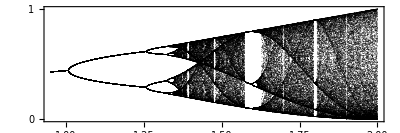

```mathematica
BifurcationPlot[r g[x],{r,0.95,2},{x,1/10},{1000,128},PlotPoints->1000,PlotRangePadding->{{0,0.03},{0.1,0.1}},FrameTicks->{Automatic,{0,1,2},None,None}]
```